```mathematica
<<Topy/vizhandmap.m
```

```mathematica
<<Topy/projections.m
```

```mathematica
rfs=readRFs["/Users/work/website/visuotopy/data/mk9RFS-edited2.txt"];
```

## Basic plotting

```mathematica
vizHandmap2[
rfs,
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->120
]
```

-Graphics-

## Use different spherical projections

The lambert projection is the default setting. You can also use the stereographic projection

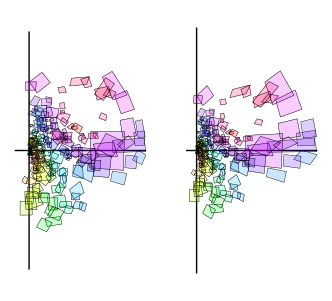

```mathematica
GraphicsRow[
Map[
vizHandmap2[
rfs,
ProjectionFunc->sphericalProjectionFunction[#],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
]&,
{"lambert","stereographic"}
]
]
```

## Change polygon styles

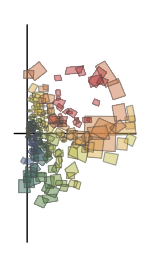

```mathematica
vizHandmap2[
rfs,
TractColorFunc->ColorData["DarkRainbow"],
PolygonStyleFunc->Function[{x},{EdgeForm[GrayLevel[0.3]],Thickness[0.005],Opacity[0.5]}],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
]
```

## Show only receptive field centers

Use HidePolygons->True to turn off plotting the receptive fields as polygons. In thise case, PolygonCenterMarkers is automatically set to be true so that the center of the receptive fields are displayed. The size the center markers can be specified by PolygonCenterMarkerStyle. By default, the colors of the center markers are set according to the tract of the receptive field. To use one single color for all markers, simply set TractColorFunc to a function that returns that color.

```mathematica
g1=vizHandmap2[
rfs,
HidePolygons->True,
TractColorFunc->ColorData["DarkRainbow"],
PolygonCenterMarkerStyle->PointSize[0.02],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
```

```mathematica
g2=vizHandmap2[
rfs,
HidePolygons->True,
TractColorFunc->Function[{x},Red],
PolygonCenterMarkerStyle->PointSize[0.02],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
```

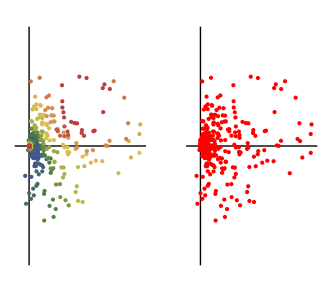

```mathematica
GraphicsRow[{g1,g2}]
```

## Show selected tracts

Use DisplayTracts to select a set of tracts. Turn on the connectors (PolygonCenterConnectors->True) and the center markers (PolygonCenterMarkers→True). The followings also demonstrates how to change the styles of the connectors and markers.

```mathematica
g1=vizHandmap2[
rfs,
DisplayTracts->{56,72},
PolygonCenterMarkers->True,
PolygonCenterConnectors->True,
PolygonCenterConnectorStyle->Directive[Black,Thickness[0.008],Dashing[0.01]],
TractColorFunc->ColorData["DarkRainbow"],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
```

```mathematica
g2=vizHandmap2[
rfs,
DisplayTracts->{56,72},
HidePolygons->True,
PolygonCenterConnectors->True,
PolygonCenterMarkerStyle->PointSize[0.05],
PolygonCenterConnectorStyle->Directive[GrayLevel[0.2],Thickness[0.008],Dashing[0.01]],
TractColorFunc->ColorData["DarkRainbow"],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
```

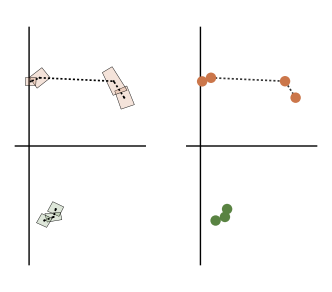

```mathematica
GraphicsRow[{g1,g2}]
```

## Construct virtual tracts

Use VirtualTracts to organize arbritrary receptive fields into “virtual tracts”.

```mathematica
vt1={"50D","29G","49B","33D","72A"};
vt2={"64D","5E","8B","42B"};
```

```mathematica
g1=vizHandmap2[
rfs,
VirtualTracts->{vt1,vt2},
PolygonCenterMarkers->True,
PolygonCenterConnectors->True,
PolygonCenterConnectorStyle->Directive[Black,Thickness[0.008],Dashing[0.01]],
TractColorFunc->ColorData["DarkRainbow"],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
g2=vizHandmap2[
rfs,
VirtualTracts->{vt1,vt2},
HidePolygons->True,
PolygonCenterMarkers->True,
PolygonCenterConnectors->True,
PolygonCenterMarkerStyle->PointSize[0.05],
PolygonCenterConnectorStyle->Directive[Black,Thickness[0.008],Dashing[0.01]],
TractColorFunc->ColorData["DarkRainbow"],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
];
```

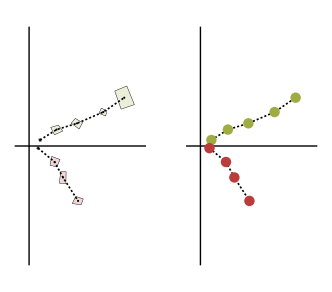

```mathematica
GraphicsRow[{g1,g2}]
```

## Show selected items

Items works best with a small number of tracts. I use VirtualTratcs to construct two virtual tracts. By default, Items is set to All, which display all receptive fields in all tracts. It can be set to a list of item selectors. The length of the list should be the same as the number of tracts. A selector can be either a list of integers or All.

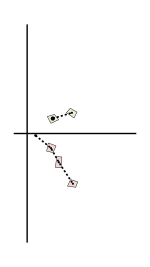

```mathematica
g1=vizHandmap2[
rfs,
VirtualTracts->{vt1,vt2},
Items->{{2,3},All},
PolygonCenterMarkers->True,
PolygonCenterConnectors->True,
PolygonCenterConnectorStyle->Directive[Black,Thickness[0.008],Dashing[0.01]],
TractColorFunc->ColorData["DarkRainbow"],
CoordIndex0->3,
CoordIndex1->-2,
LongitudeRange->{-10Degree,90Degree},
ImageSize->150
]
```